```mathematica
func[x_]:=Log[Exp[x]-1]
```

```mathematica
<<FunctionApproximations`
```

```mathematica
x0=0
x1=0.001
x2=0.01
x3=0.1
x4=1.0
```

0

0.001

0.01

0.1

1.

```mathematica
approx1=RationalInterpolation[func[x],{x,4,4},{x,x1,x2}]
```

(-9.7609-29524.9 x-1.1896×10^7 x^2-7.8606×10^8 x^3-2.7958×10^9 x^4)/(1+4115.76 x+2.19207×10^6 x^2+2.13582×10^8 x^3+2.69117×10^9 x^4)

```mathematica
approx2=RationalInterpolation[func[x],{x,4,4},{x,x2,x3}]
```

(-7.44413-1957.46 x-63820.7 x^2-227666. x^3+431986. x^4)/(1+403.963 x+20798.1 x^2+188119. x^3+180043. x^4)

```mathematica
approx3=RationalInterpolation[func[x],{x,4,4},{x,x3,x4}]
```

(-5.14322-101.762 x-127.318 x^2+317.316 x^3+135.057 x^4)/(1+40.3169 x+202.816 x^2+160.947 x^3-2.08876 x^4)

```mathematica
fullapprox[x_]:=If[x>x4,func[x],If[x>x3,approx3,func[x]]]
```

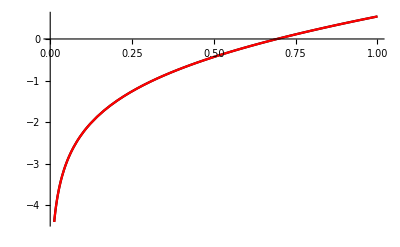

```mathematica
Plot[{func[x],fullapprox[x]},{x,x1,x4},PlotStyle->{Black,Red}]
```

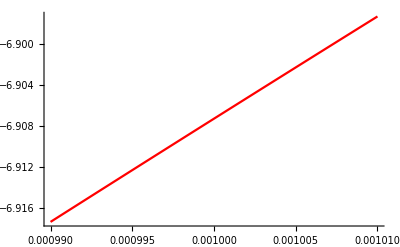

```mathematica
Plot[fullapprox[x],{x,0.99*x1,1.01*x1},PlotStyle->{Black,Red}]
```

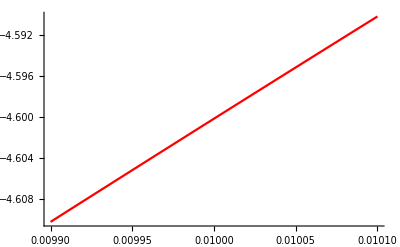

```mathematica
Plot[fullapprox[x],{x,0.99*x2,1.01*x2},PlotStyle->{Black,Red}]
```

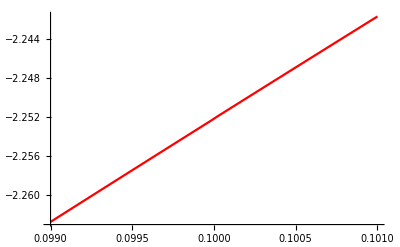

```mathematica
Plot[fullapprox[x],{x,0.99*x3,1.01*x3},PlotStyle->{Black,Red}]
```

```mathematica
adiff[x_]:=fullapprox[x]-func[x]
```

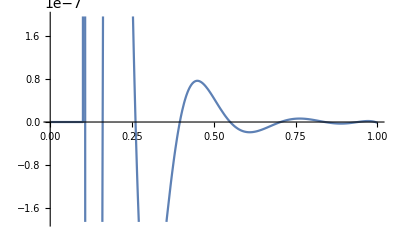

```mathematica
Plot[adiff[x],{x,x1,x4}]
```

```mathematica
pdiff[x_]:=100*(fullapprox[x]-func[x])/func[x]
```

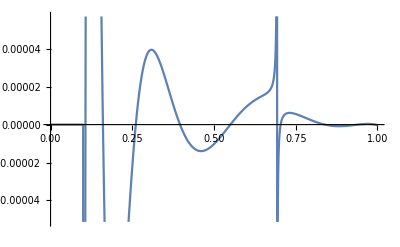

Plot[pdiff[x],{x,x,x4}]

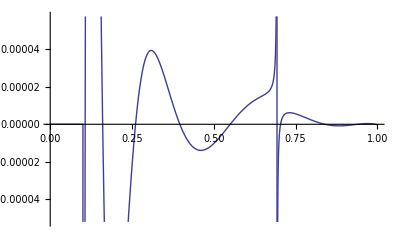

```mathematica
Plot[pdiff[x],{x,x0,x4}]
```

```mathematica
CForm[approx1]
```

(-9.760898531545386 - 29524.941133033215*x - 1.1896019336956682e7*Power(x,2) - 
     7.860596631970513e8*Power(x,3) - 2.795797091759987e9*Power(x,4))/
   (1 + 4115.755490541176*x + 2.19207068008156e6*Power(x,2) + 
     2.1358160394371653e8*Power(x,3) + 2.6911720709828815e9*Power(x,4))

```mathematica
CForm[approx2]
```

(-7.4441271863249625 - 1957.455251107371*x - 63820.69082039389*Power(x,2) - 
     227666.32263762745*Power(x,3) + 431986.40491931344*Power(x,4))/
   (1 + 403.96307514244734*x + 20798.07111653145*Power(x,2) + 
     188119.3222406968*Power(x,3) + 180043.28571064543*Power(x,4))

```mathematica
CForm[approx3]
```

(-5.143220028201872 - 101.76227310588246*x - 127.31825068394369*Power(x,2) + 
     317.31602891172594*Power(x,3) + 135.0567120741147*Power(x,4))/
   (1 + 40.31685825976414*x + 202.81583582446692*Power(x,2) + 
     160.94697665742055*Power(x,3) - 2.088756969431516*Power(x,4))